## 1N

Zbudowano wielomian interpolacyjny oparty na nastepujacych danych:

```mathematica
XY={{0.06250,0.687959},{0.187500,0.073443},{0.312500,-0.517558},{0.437500,-1.077264},{0.562500,-1.600455},{0.687500,-2.080815},{0.812500,-2.507266},{0.935700,-2.860607}};
```

```mathematica
Lagrange[XY_,rozm_]:=
Module[{n=rozm-1,wyn,suma=0,resz,X,Y},
X =Transpose[XY]_⟦1⟧;
Y = Transpose[XY]_⟦2⟧; 
Do[wyn = 1; 
Do[ resz = Which[ j==k, 1,
j≠k,(x - X_⟦j+1⟧)/(X_⟦k+1⟧-X_⟦j+1⟧) ]; 
wyn= wyn*resz; ,{j,0,n,1}]; 
suma = suma+ Y_⟦k+1⟧*wyn; ,{k,0,n,1}]; 

Return[Print["Wielomian interpolacyjny: "];
Expand[suma]]; ];
```

Wielomian interpolacyjny:

1.00104-5.03245 x+0.348127 x^2+0.199569 x^3+3.03844 x^4-6.80247 x^5+6.28258 x^6-2.05026 x^7

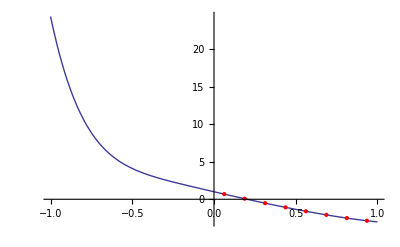

```mathematica
y=Lagrange[XY,8]
Show[Plot[y,{x,-1,1}],ListPlot[XY,PlotStyle->{Red,PointSize[Medium]}]]
```